```mathematica
data = {{0.04558029,2.38210000},{0.00000000,2.51200000}}
```

{{0.0455803,2.3821},{0.,2.512}}

```mathematica
parabola = Fit[data,{1,x^2},x]
```

2.512-62.5252 x^2

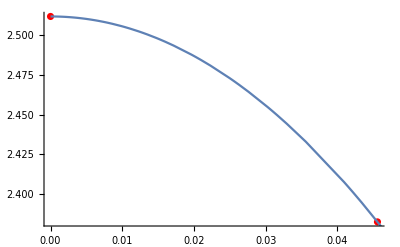

```mathematica
Show[ListPlot[data, PlotStyle->Red],Plot[parabola,{x,0,1}]]
```

```mathematica
data2 = {{0.00000000,2.51200000},{0.03721615,2.42100000}}
```

{{0.,2.512},{0.0372162,2.421}}

```mathematica
parabola2 = Fit[data2,{1,x^2},x]
```

2.512-65.702 x^2

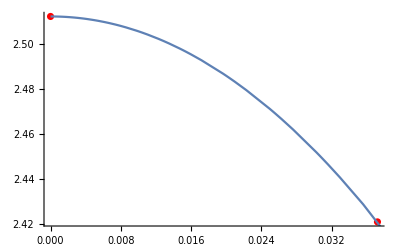

```mathematica
Show[ListPlot[data2, PlotStyle->Red],Plot[parabola2,{x,0,1}]]
```

```mathematica
data3 = {{0.02631579,2.46370000},{0.00000000,2.51200000}}
```

{{0.0263158,2.4637},{0.,2.512}}

```mathematica
parabola3= Fit[data3,{1,x^2},x]
```

2.512-69.7452 x^2

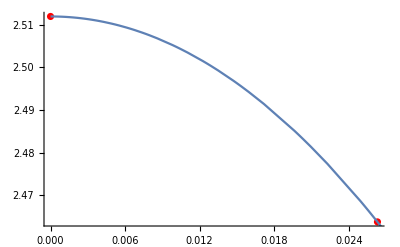

```mathematica
Show[ListPlot[data3, PlotStyle->Red],Plot[parabola3,{x,0,1}]]
```

```mathematica
(62.52+65.70+69.74)/3
```

65.9867

```mathematica
Subscript[E, 0]=1.602176487*^-19
a = 6.28*^-10
m = 9.10938215*^-31
Subscript[E, 0]/(2*3.14/a)^2
ℏ = 1.054571628251774*^-34
```

1.60218×10^-19

6.28×10^-10

9.10938×10^-31

1.60218×10^-39

1.05457×10^-34

```mathematica
(1.054571628251774*^-34)^2/(66*Subscript[E, 0]/(2*3.14/a)^2)/(2m)
```

0.057727